```mathematica
pendulumwaves[n_,Γ_,pendula_,t_,amp_,op_,v_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp,sol,x},g=9.8;lengths=Table[100 g(Γ/(2π(n+x)))^2,{x,0,pendula-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula,-5,0},{5+2 pendula,5,0},{5+2 pendula,5,2},{5+2 pendula,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula,5,0},{5+2 pendula,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula,5,2},{5+2 pendula,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula,-5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op],Texture[-Graphics-]}];
vp=v/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],AbsolutePointSize[15],Point[{5+2i,amp Cos[(20π t)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[(20π t)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}]},{i,1,pendula}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp Cos[(20π t)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[(20π t)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}}],{i,1,pendula}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t];Show[display,post]]
```

```mathematica
pendulumwaves2[n_,Γ_,pendula_,t_,amp_,op_,v_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp},g=9.8;lengths=Table[100 g(Γ/(2π(n+x)))^2,{x,0,pendula-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula,-5,0},{5+2 pendula,5,0},{5+2 pendula,5,2},{5+2 pendula,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula,5,0},{5+2 pendula,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula,5,2},{5+2 pendula,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula,-5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op],Texture[-Graphics-]}];
vp=v/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],AbsolutePointSize[15],Point[{5+2i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}]},{i,1,pendula}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}}],{i,1,pendula}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t];Show[display,post]]
```

### Hooke’s Law - linear approximation

I begin with the pendula undergoing motion according to the Hooke’s law approximation for small angles.  The full physical restoring force will be modeled subsequently.  This model lines up fairly well with the video demonstration of the actual apparatus due to the small amplitudes in the oscillations of the pendula in the video.

```mathematica
pendulumwaves2[n_,Γ_,pendula_,t_,amp_,op_,v_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp},g=9.8;lengths=Table[100 g(Γ/(2π(n+x)))^2,{x,0,pendula-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula,-5,0},{5+2 pendula,5,0},{5+2 pendula,5,2},{5+2 pendula,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula,5,0},{5+2 pendula,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula,5,2},{5+2 pendula,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula,-5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op],Texture[-Graphics-]}];
vp=v/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],AbsolutePointSize[15],Point[{5+2i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}]},{i,1,pendula}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}}],{i,1,pendula}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t];Show[display,post]];Manipulate[pendulumwaves2[50,60,q,t,amp,op,v],{{t,0,"time"},0,60,ControlType->Animator,AnimationRunning->False,AnimationRate->1},{{amp,4,"amplitude"},0,21.1515},{{q,15,"pendula"},15,40},Row[{Control@{{v,0,"view"},{0->"front",1->"side", 2-> "top"},Setter},Spacer[25],Control@{{op,1,"opacity"},{1->"opaque",.5->"translucent", 0-> "transparent"},Setter}}],SaveDefinitions->True]
```

```mathematica
n=50;Γ=60;g=9.8;amp=6;
```

```mathematica
lengths=Table[{100 g(Γ/(2π(n+1+x)))^2},{x,0,14}]
```

{{34.358},{33.0493},{31.8139},{30.6465},{29.5422},{28.4966},{27.5055},{26.5652},{25.6723},{24.8237},{24.0165},{23.248},{22.5158},{21.8177},{21.1515}}

```mathematica
sample = {0,Γ/8,(4Γ)/16,(7Γ)/16,Γ/2,(9Γ)/16,(12Γ)/16,(7Γ)/8,Γ};pendula=15;
```

### Apparent cyclical activity

If you observe the positions of the pendula below, taken at different times throughout one full cycle (in this case a cycle was made to be 60 seconds), you will see that the patterns apparently repeat themselves after the halfway point.  At 60 seconds the pendula have apparently run the same patterns in reverse order and returned to their starting point.

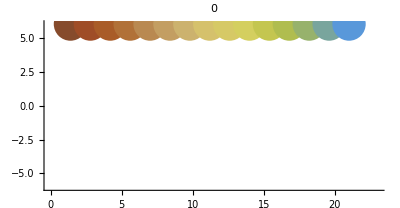
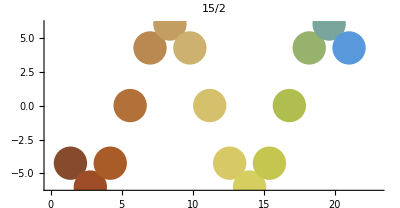
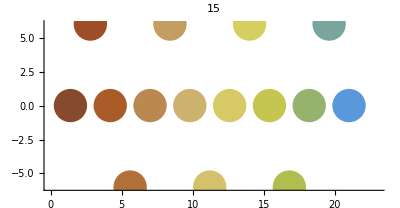
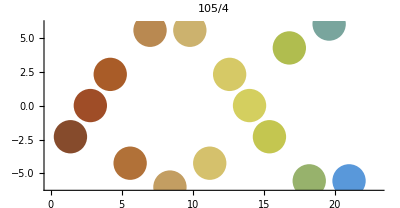
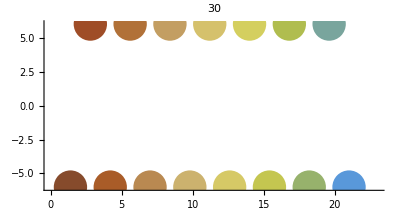
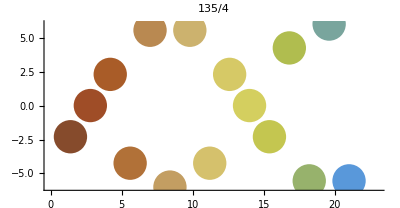
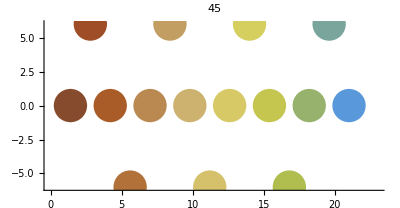
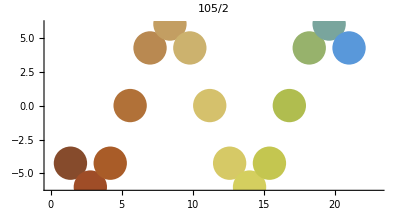

```mathematica
Table[Graphics[{PointSize[.06],Table[{ColorData["SouthwestColors"][i/15],Point[{1.4i,amp Cos[((n+i)2π sample⟦t⟧)/Γ] }]},{i,1,15}]},PlotRange->{{0,23},{-6,6}},Axes->True,PlotLabel->sample⟦t⟧],{t,1,9}]
```

### Continuous underlying function

From the first article referenced in the reference section of this project, they were able to derive a continuous, non cyclical underlying function describing the positions of all the pendula throughout the cycle.  With this function being non-cyclical the question arises as to why the patterns apparently repeat in a cyclical manner.  The function below is the function modeling the positions of all the pendula simultaneously, it looks like a traveling sine wave that continuously shortens its wavelength with constant amplitude.

```mathematica
Animate[Plot[{5 Cos[((2π)t/(1.4 Γ))x+ 2 π n/Γ t]},{x,0,(1.4 pendula)+1},PlotRange->{{0,(1.4 pendula)+1},{-6,6}}],{t,0,60},AnimationRate->1,AnimationRunning->False]
```

### Aliasing

The table below reveals the nature of this paradox.  Showing the underlying function along with the positions of the pendula reveals that although the pendula apparently undergo cyclical pattern activity, the underlying function is actually getting increasingly complex.  The apparent cyclical activity is a result of aliasing.  A familiar form of aliasing occurs in video footage of something like a helicopter blade or a car wheel, where the framerate of the camera is insufficient to capture the full motion of the rotating object, causing it to appear as if it is moving backwards for example.  However, what is occurring in this case is slightly different.  The framerate example is a result of temporal aliasing, the framerate is insufficient with regards to time.  In our case it is spatial aliasing, there are not enough pendula to describe the complexity of the underlying function.  This will be demonstrated next.

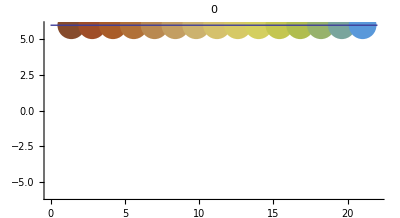
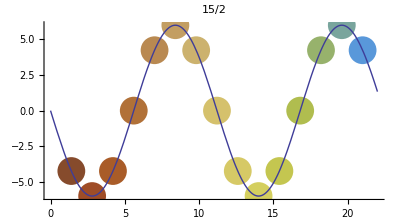
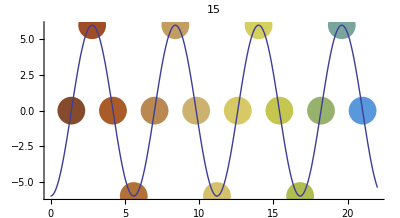
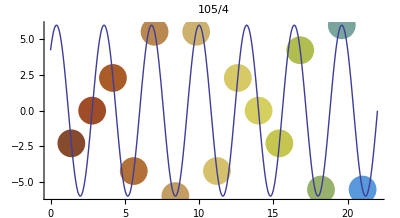
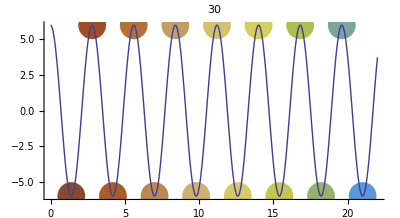
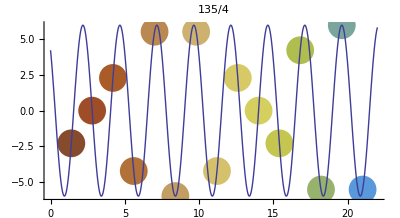
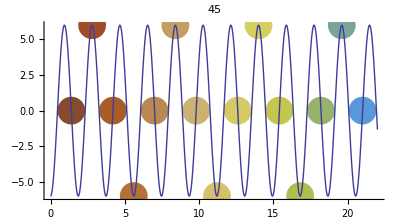
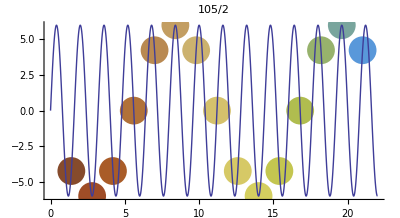

```mathematica
Table[Show[{Graphics[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],Point[{1.4i,amp Cos[((n+i)2π sample⟦t⟧)/Γ] }]},{i,1,pendula}]},PlotRange->{{0,(1.4 pendula)+1},{-6,6}},Axes->True,PlotLabel->sample⟦t⟧],Plot[{amp Cos[((2π)sample⟦t⟧/(1.4 Γ))x+ 2 π n/Γ sample⟦t⟧]},{x,0,(1.4 pendula)+1}]}],{t,1,9}]
```

### Animation

This animation shows that the pendula positions are indeed accurately modeled by the underlying function.

```mathematica
Animate[Show[{Graphics[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],Point[{1.4i,5 Cos[((n+i)2π t)/Γ] }]},{i,1,pendula}]},PlotRange->{{0,(1.4 pendula)+1},{-6,6}},Axes->True],Plot[{5 Cos[((2π)t/(1.4 Γ))x+ 2 π n/Γ t]},{x,0,(1.4 pendula)+1}]}],{t,0,60},AnimationRate->1,AnimationRunning->False]
```

### Aliasing continued

The pendula in the previous plots are modeled again here, with all of the ones plotted previously now shown in red.  I have included additional pendula, plotted in blue, at positions in between the pendula that were previously plotted.  As you can see, while the red pendula still undergo apparent cyclical activity, with the inclusion of the blue pendula it is obvious that the positions of all pendula are not repeated in this manner.

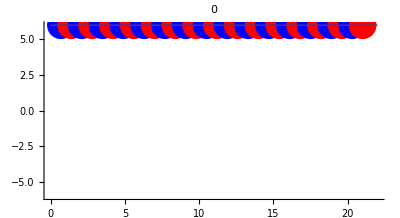
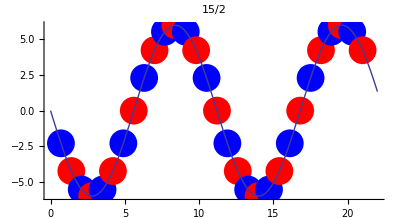
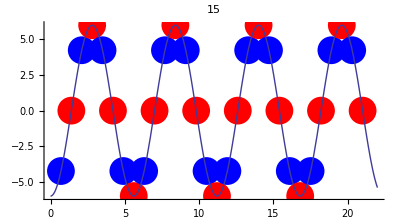
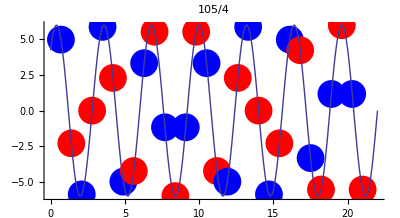
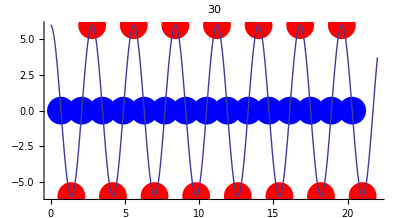
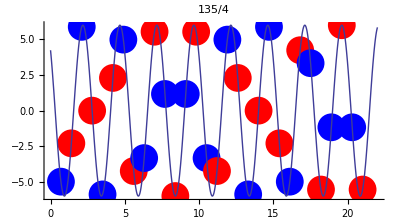
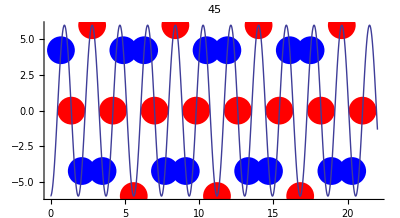
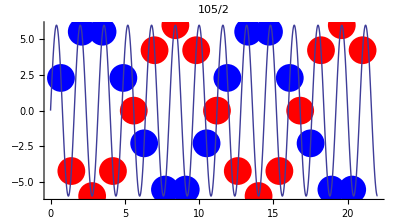

```mathematica
Table[Show[{Graphics[{PointSize[.05],Table[{If[Mod[i,2]==0,Red,Blue],Point[{1.4 i/2,amp Cos[((n+i/2)2π sample⟦t⟧)/Γ] }]},{i,1,2pendula}]},PlotRange->{{0,(1.4 pendula)+1},{-6,6}},Axes->True,PlotLabel->sample⟦t⟧],Plot[{amp Cos[((2π)sample⟦t⟧/(1.4 Γ))x+ 2 π n/Γ sample⟦t⟧]},{x,0,(1.4 pendula)+1}]}],{t,1,9}]
```

### Full restoring force

This time I have modeled the motion of the pendula using the more accurate full restoring force that changes with amplitude.  It was modeled using the elliptic integrals built in to Mathematica.  You can see that the motions deviate from the model using the small angle approximation as you increase the amplitude.  The pendula with the shortest lengths are affected the most because the angle between the point where they are attached at the top and the bob at the peak of an oscillation is greater than that for a longer pendulum.

```mathematica
pendulumwaves[n2_,Γ2_,pendula2_,t2_,amp2_,op2_,v2_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp,sol,x},g=9.8;lengths=Table[100 g(Γ2/(2π(n2+x)))^2,{x,0,pendula2-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula2,-5,0},{5+2 pendula2,5,0},{5+2 pendula2,5,2},{5+2 pendula2,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula2,-5,2},{5+2 pendula2,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula2,5,0},{5+2 pendula2,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula2,5,2},{5+2 pendula2,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula2,-5,2},{5+2 pendula2,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula2,-5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧},{5+2 pendula2,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op2],Texture[-Graphics-]}];
vp=v2/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula2],AbsolutePointSize[15],Point[{5+2i,amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}]},{i,1,pendula2}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}}],{i,1,pendula2}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op2,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula2+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t2];Show[display,post]];Manipulate[pendulumwaves[50,60,q2,t2,amp2,op2,v2],{{t2,0,"time"},0,60,ControlType->Animator,AnimationRunning->False,AnimationRate->1},{{amp2,6,"amplitude"},0,18.07582840696849},{{q2,15,"pendula"},15,40},Row[{Control@{{v2,0,"view"},{0->"front",1->"side", 2-> "top"},Setter},Spacer[25],Control@{{op2,1,"opacity"},{1->"opaque",.2->"translucent", 0-> "transparent"},Setter}}],SaveDefinitions->True]
```

### Side by side comparison

This is a comparison of the two models.  I have started it at the 30 second mark and you can see the deviation from the small angle approximation by comparing the two.

```mathematica
pendulumwaves[n2_,Γ2_,pendula2_,t2_,amp2_,op2_,v2_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp,sol,x},g=9.8;lengths=Table[100 g(Γ2/(2π(n2+x)))^2,{x,0,pendula2-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula2,-5,0},{5+2 pendula2,5,0},{5+2 pendula2,5,2},{5+2 pendula2,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula2,-5,2},{5+2 pendula2,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula2,5,0},{5+2 pendula2,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula2,5,2},{5+2 pendula2,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula2,-5,2},{5+2 pendula2,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula2,-5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula2,5,1.2 lengths⟦1⟧},{5+2 pendula2,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧+3},{5+2 pendula2,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧+3},{5+2 pendula2,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op2],Texture[-Graphics-]}];
vp=v2/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula2],AbsolutePointSize[15],Point[{5+2i,amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}]},{i,1,pendula2}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp2 Cos[(20π t2)/(4 EllipticK[Sin[ArcSin[amp2/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))])^2)}}],{i,1,pendula2}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op2,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula2+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t2];Show[display,post]];pendulumwaves2[n_,Γ_,pendula_,t_,amp_,op_,v_]:=
Module[{g,lengths,display,post,vtc,bottom,top,vp},g=9.8;lengths=Table[100 g(Γ/(2π(n+x)))^2,{x,0,pendula-1}]; 
vtc={{0,0},{1,0},{1,1},{0,1}};
bottom={{{-6,-5,0},{-6,5,0},{-6,5,2},{-6,-5,2}},{{5+2 pendula,-5,0},{5+2 pendula,5,0},{5+2 pendula,5,2},{5+2 pendula,-5,2}},{{-6,5,2},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,5,2}},{{-6,-5,0},{-6,5,0},{5+2 pendula,5,0},{5+2 pendula,-5,0}},{{-6,5,0},{-6,5,2},{5+2 pendula,5,2},{5+2 pendula,5,0}},{{-6,-5,0},{-6,-5,2},{5+2 pendula,-5,2},{5+2 pendula,-5,0}}};
top={{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3}},{{5+2 pendula,-5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3}},{{-6,5,1.2 lengths⟦1⟧+3},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3}},{{-6,-5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧},{5+2 pendula,5,1.2 lengths⟦1⟧},{5+2 pendula,-5,1.2 lengths⟦1⟧}},{{-6,5,1.2 lengths⟦1⟧},{-6,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧+3},{5+2 pendula,5,1.2 lengths⟦1⟧}},{{-6,-5,1.2 lengths⟦1⟧},{-6,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧+3},{5+2 pendula,-5,1.2 lengths⟦1⟧}}};
post=RevolutionPlot3D[{{3,r}},{r,0,1.2lengths⟦1⟧},{θ,0,2π},Mesh->None,TextureCoordinateFunction->({#1,#2}&),PlotStyle->{Opacity[op],Texture[-Graphics-]}];
vp=v/. {0->{5,0  ,0 }, 1->{0,∞  ,0 },2 ->{0,0,∞ }};
display= Graphics3D[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],AbsolutePointSize[15],Point[{5+2i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}]},{i,1,pendula}],Table[Line[{{5+2i,0,1.2lengths⟦1⟧},{5+2 i,amp Cos[((n+i)2π t)/Γ], 1.2lengths⟦1⟧-√(lengths⟦i⟧^2-(amp Cos[((n+i)2π t)/Γ])^2)}}],{i,1,pendula}],Brown,Specularity[White,5],Lighting->{{"Point",White,Scaled[{1,3,-2}]}},Texture[-Graphics-],Opacity->op,Polygon[top,VertexTextureCoordinates->Table[vtc,{6}]],Lighting->{{"Point",White,Scaled[{1,3,5}]}},Polygon[bottom,VertexTextureCoordinates->Table[vtc,{6}]]},PlotRange->{{-7,5+2 pendula+1},{-24 ,24 },{-0,1.4lengths⟦1⟧}},Axes->True,ViewPoint->vp,ImageSize->400,PlotLabel->t];Show[display,post]];Manipulate[{pendulumwaves[50,60,q,t,amp,op,v],pendulumwaves2[50,60,q,t,amp,op,v]},{{t,30,"time"},0,60,ControlType->Animator,AnimationRunning->False,AnimationRate->.5},{{amp,4.68,"amplitude"},0,18.07582840696849},{{q,15,"pendula"},15,40},Row[{Control@{{v,0,"view"},{0->"front",1->"side", 2-> "top"},Setter},Spacer[25],Control@{{op,1,"opacity"},{1->"opaque",.2->"translucent", 0-> "transparent"},Setter}}],SaveDefinitions->True]
```

### Deviation from underlying function

These plots demonstrate how the model using the full restoring force deviates from the underlying function that was worked out for the small angle approximation.

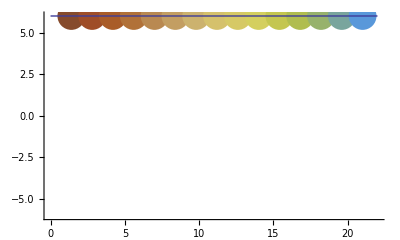
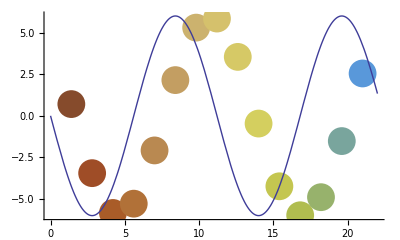
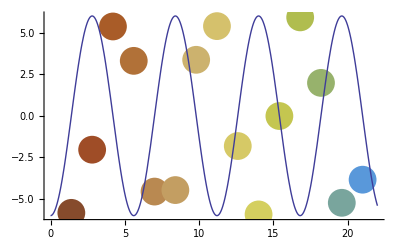
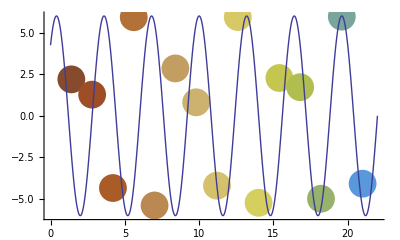
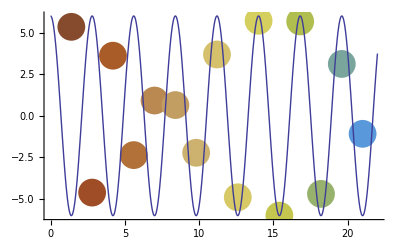
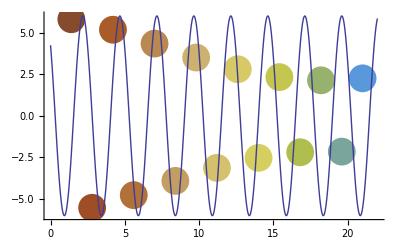
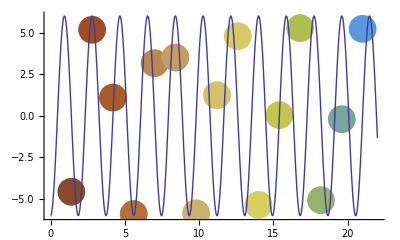
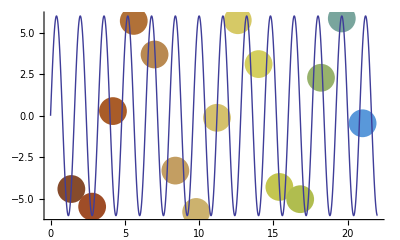

```mathematica
Table[Show[{Graphics[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],Point[Flatten[{{1.4i},amp Cos[(20π sample⟦t⟧)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))] }]]},{i,1,pendula}]},PlotRange->{{0,(1.4 pendula)+1},{-amp,amp}},Axes->True],Plot[{amp Cos[((2π)sample⟦t⟧/(1.4 Γ))x+ 2 π n/Γ sample⟦t⟧]},{x,0,(1.4 pendula)+1}]},AspectRatio->.6],{t,1,9}]
```

### Deviation from underlying function continued

Below i have an animation of the positions of the pendula using the full restoring force along with the underlying function using the small angle approximation.  As you can see, if you decrease the amplitude, the deviation from the function becomes smaller.  With a sufficiently small amplitude, there is practically no deviation.

```mathematica
Manipulate[Show[{Graphics[{PointSize[.05],Table[{ColorData["ValentineTones"][i/pendula],Point[Flatten[{{1.4i},amp Cos[(20π t)/(4 EllipticK[Sin[ArcSin[amp/lengths⟦i⟧]/2]] √(lengths⟦i⟧/g))] }]]},{i,1,pendula}]},Axes->True,PlotRange->{{0,1.4 pendula},{-1.3amp,1.3amp}}]},{Graphics[{PointSize[.05],Table[{ColorData["SouthwestColors"][i/pendula],Point[{1.4i,amp Cos[((n+i)2π t)/Γ] }]},{i,1,pendula}]},Axes->True],Plot[{amp Cos[((2π)t/(1.4 Γ))x+ 2 π n/Γ t]},{x,0,(1.4 pendula)+1}]},ImageSize->{400,350},AspectRatio->.5],{{t,0,"time"},0,Γ,ControlType->Animator,AnimationRunning->False,AnimationRate->1},{{amp,6,"amplitude"},0,10}]
```

```mathematica
Series[EllipticK[x],{x,0,9}]
```

π/2+(π x)/8+(9 π x^2)/128+(25 π x^3)/512+(1225 π x^4)/32768+(3969 π x^5)/131072+(53361 π x^6)/2097152+(184041 π x^7)/8388608+(41409225 π x^8)/2147483648+(147744025 π x^9)/8589934592+O[x]^10

```mathematica
sol=Table[Solve[(51+i) 4(π/2+(π x)/8+(9 π x^2)/128+(25 π x^3)/512+(1225 π x^4)/32768+(3969 π x^5)/131072+(53361 π x^6)/2097152+(184041 π x^7)/8388608+(41409225 π x^8)/2147483648+(147744025 π x^9)/8589934592)√(x/9.8)==60,x]⟦5⟧,{i,0,15-1}]
```

{{x→0.290475},{x→0.281162},{x→0.272255},{x→0.263736},{x→0.255584},{x→0.247779},{x→0.240305},{x→0.233145},{x→0.226282},{x→0.219701},{x→0.213388},{x→0.207331},{x→0.201515},{x→0.19593},{x→0.190564}}

```mathematica
Solve[100 9.8(60/(2π(y)))^2==29.04753816797735,y]⟦2⟧
```

{y→55.4664}

## References

### Pendulum waves: A lesson in aliasing James A. Flatena) and Kevin A. Parendo Division of Science and Mathematics, University of Minnesota–Morris, Morris, Minnesota 56267

### -Graphics-

### Wikipedia pendulum article